## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData,i},
gridLabel={"k","(X^k)","f(X^k)","r"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
gridData[[All,4]]=SetAccuracy[norms,4];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,limit_,setX_,setY_,{points_,fValues_}]:=Module[{},
Show[ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}],ContourPlot[limit[{x,y}]==0,setX,setY,ContourStyle->Black],ContourPlot[limit[{x,y}]==-0.05,setX,setY,ContourStyle->Red]]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
Antigrad[point_, func_] := -Grad[func[{x, y}], {x, y}] /. {x->point[[1]],y->point[[2]]};
Hesse[ func_] := D[func[{x,y}],{{x,y},2}] ;
CalcHesse[MHesse_,{xp_,yp_}]:=MHesse/.{x -> xp, y -> yp};
MakePositive[Hesse_,k_]:=Module[{H = Hesse,n = Length@Hesse},
If[PositiveDefiniteMatrixQ[Hesse],
Return[H],
H = MakePositive[H+k*IdentityMatrix[n],k];
];
Return[H]
];
```

## Алгоритм

```mathematica
Algorithm[point_,f_,g_,ϵ_,Cond_] := Module [{points={0,point},values={0,f[point]},r={1},result},
While[Abs[values⟦-1⟧-values⟦-2⟧]≥ϵ||Abs[points⟦-1⟧-points⟦-2⟧]≥ϵ,
If[Cond==True,
result = FindMinimum[f[{x,y}]+Piecewise[{{0,g[{x,y}]<0}},r⟦-1⟧*(g[{x,y}])^2],{{x,points⟦-1,1⟧},{y,points⟦-1,2⟧}}],
result = FindMinimum[f[{x,y}]+Piecewise[{{-r⟦-1⟧/g[{x,y}],g[{x,y}]<0}},1/r⟦-1⟧-r⟦-1⟧/g[{x,y}]],{{x,points⟦-1,1⟧},{y,points⟦-1,2⟧}}];
];
AppendTo[points,{result[[2,1,2]],result[[2,2,2]]}];
AppendTo[values,result⟦1⟧];
If[Cond==True,
AppendTo[r,r⟦-1⟧*2],
AppendTo[r,r⟦-1⟧/2];
];
];
{points,values,r}
];
```

## Функции:

```mathematica
(*3/4 x^2+5/4 x-2-y;*)
```

```mathematica
g[{x_,y_}]:=x^2+y;
rosenbrok[{x_,y_}]:=(1-x)^2+(y-x^2)^2;
```

## Вычисления:

```mathematica
ϵ=10^-3;
```

### Первый пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
Res = Algorithm[{-1,-2},func,g,ϵ,True];
X= Res[[1,2;;]];
val= Res[[2,2;;]];
r = Res[[3]];
setX = {x,-4,4};
setY ={y,-4,4};
```

### Второй пример:

## Результаты:

```mathematica
MakeTable[{X,val,r}]
```

k | (X^k) | f(X^k) | r
0 | ( -1.000, -2.000 ) | 13. | 1.
1 | ( 0.500, 0. ) | 0.375 | 2.
2 | ( 0.465, -0.072 ) | 0.411 | 4.
3 | ( 0.443, -0.118 ) | 0.433 | 8.
4 | ( 0.431, -0.144 ) | 0.446 | 16.
5 | ( 0.424, -0.159 ) | 0.453 | 32.
6 | ( 0.421, -0.167 ) | 0.457 | 64.
7 | ( 0.419, -0.170 ) | 0.459 | 128.
8 | ( 0.418, -0.172 ) | 0.46 | 256.

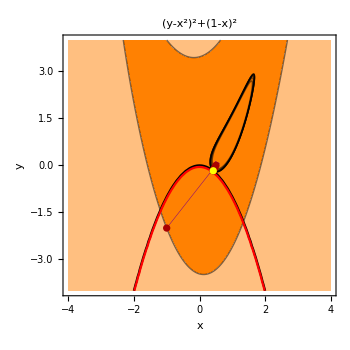

```mathematica
PlotMethod[func,g,setX,setY,{X,val}]
```